Stephanie idea version 2: Does not seem to really matter what βϵ_R is, but it is probably positive

-Graphics-

Stephanie idea version 1: βϵ_R=4.5
(This did not consider the effect of the operator itself pulling more of the repressors into the active state)

#### Future Ideas

To get uncertainty in the x-coordinate in play, can start by looking here

## Stephanie’s Idea - Calculating ⅇ^-βϵ_R

See email "LacI Data Fitting and Sloppiness" on 2016-06-29

The basic idea is that when you have multiple promoters with copy number N>1, the fold-change equation allows you to actually fit the ⅇ^-βϵ_R parameter, since it shifts the resulting fold-change curve to the right as ϵ_R decreases.

fold-change=(∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA)(N-m))/(N∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA))

R_eff=1/(1+ⅇ^-βϵ_R)R_tot

βϵ_DNA=βϵ_DNA^Hernan+Log[1/(1+ⅇ^-βϵ_R)]

#### Code

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=E(*N[E]*)},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
(* Plot has a hard time with this function, because the Min naturally makes the plot bumpy, which is hard to calculate precisely *)
(*LogLogPlot[{foldChange[10.,r,-2.,-17.],foldChange[10.,r,2.,-17.]},{r,10^0,10^3},PerformanceGoal->"Speed"]*)
```

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
relabel@ListLogLogPlot[data,Joined->True,PlotLegends->("βϵ_R="<>ToString@#&/@βϵValues),FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),opts]
```

-Graphics-

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
leg=LineLegend[ColorData[97]/@Range@Length@βϵValues,font[#,10]&/@("βϵ_R="<>ToString@#&/@βϵValues),Spacings->{0.5,0.2}];
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
ListLogLogPlot[data,Joined->True,PlotLegends->leg,FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"})(*,FrameTicks->{LogTicks[10^0,10^3,TickLengthScale->2],LogTicks[10^-4,10^0,TickLengthScale->2]}*),opts]
```

-Graphics-

Next question: Fit the Franz data to obtain the best fit βϵ_R. Tell Stephanie (and then ask for her input before passing it onto Rob, Manuel, Griffin), emphasizing that this is a 1-parameter fit only, so it should nail down βϵ_R very well.
The one downside is that I don’t have the error bars from Franz’s data, which may slightly modify the βϵ_R but probably not too much

### Fitting ⅇ^-βϵ_R

#### Visualize the Data

```mathematica
colors={Black,Red,Darker@Green,Blue,Black,Red,Darker@Green,Blue,Purple,Darker@Yellow,Lighter[Blue,0.6],Black,Red,Blue};
markers=Flatten[{Table["◇",{4}],Table["●",{4}],Table["●",{3}],,Table["□",{3}]},1];
With[{opts=opts},
ListLogLogPlot[data,PlotRange->{{10^0,10^3.5},{10^-4.5,10^0.5}},FrameLabel->{"Repressor Copy Number","Fold-Change"},PlotStyle->colors,PlotMarkers->markers,AspectRatio->1,Frame->True,FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},ImageSize->Medium,FrameStyle->Black,FrameTicksStyle->Black,Prolog->{},opts]
]
```

#### 1st try - Assuming all repressors are in active state

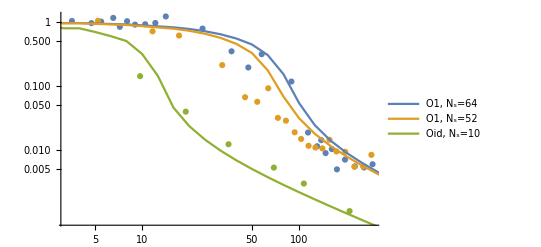

```mathematica
βϵR=1.;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

```mathematica
foldChange2[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=E(*N[E]*)},
With[{sumMin=If[n<rEff,n,rEff]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,sumMin}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,sumMin}])
]
]
```

```mathematica
foldChange3[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=E(*N[E]*)},
If[n<rEff,
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,n}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,n}]),
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,rEff}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,rEff}])
]
]
```

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx"];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];

βϵR=10.;
newData=Transpose@Table[{{10^rLog,foldChange3[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange3[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange3[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

Next steps: I think that I need to get the error measurements for these points (at least), and then try to implement fitting using both the error in x- and y-coorindates!!!
They plotted relative error (http://faculty.washington.edu/stuve/log_error.pdf), which is why their error bars were symmetric. Need to make sure that I have a good grip on what that means
By eye, it looks pretty apparent that ⅇ^-βϵ≪1 with βϵ>10

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange3[10,R,βϵR,-17.]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Log[6.464-3.57]
Log[3.57-1.971]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange3[52,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange3[64,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

#### 2nd try - Fitting separately and without error

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
βϵR=1.;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

-Graphics-

Next steps: I think that I need to get the error measurements for these points (at least), and then try to implement fitting using both the error in x- and y-coorindates!!!
They plotted relative error (http://faculty.washington.edu/stuve/log_error.pdf), which is why their error bars were symmetric. Need to make sure that I have a good grip on what that means
By eye, it looks pretty apparent that ⅇ^-βϵ≪1 with βϵ>10

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

{0.978096,{βϵR→7.50562}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

{0.95619,{βϵR→21.7099}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{0.967162,{βϵR→2.19857}}

#### 3rd try - Fitting separately and with error

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
βϵR=1.;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

-Graphics-

```mathematica
errorData=acquire[rawData,index,"x with Error"];
```

```mathematica
weights=(Log[#[[2,2]]]-Log[#[[1,2]]])#[[1,2]]&/@Transpose@#&/@Transpose@{data[[9;;11]],errorData}
```

{{0.0927624,0.090985,0.125922,0.224065,0.0912894,0.126901,0.121469,0.0786689,0.112172,0.246552,0.124083,0.0564001,0.0229912,0.0379235,0.0356136,0.00407185,0.00226817,0.00265515,0.00196238,0.00264806,0.00171219,0.00185115,0.00209224,0.002312,0.00197245},{0.148922,0.118406,-1.32215,0.029636,0.00825736,0.00756154,0.020058,0.00508867,0.00460838,0.00268839,0.00254787,0.00187046,0.00195346,0.00190635,0.00249974,0.00135477,0.00156738,0.00163972,0.000923952,0.00115173},{0.0223528,0.00737844,0.00204013,0.00139566,0.00107779,0.000720672}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,7.5}},R,Weights->1/weights[[3]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

{0.869479,{βϵR→2.56839}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R,Weights->1/weights[[2]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

{0.465605,{βϵR→23.7643}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,2.}},R,Weights->1/weights[[1]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

{0.942495,{βϵR→21.3951}}

#### 4th try - Fitting together and without error

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
βϵR=4.525127;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,Joined->True,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
plot1=Labeled[With[{opts=opts},
Show[LogLogPlot[10^10,{x,10^0,10^3},PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],PlotRange->{{10^0,10^3},{10^-3.5,10^0.2}},FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},Evaluate@opts],ListLogLogPlot[newData,Joined->True(*,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"})*)(*,FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},opts*)],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
],aLabel,{{Top,Left}}]
```

-Graphics-A

```mathematica
d=Transpose@data[[9]];
fullData1=Transpose@Join[{Table[64.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[10]];
fullData2=Transpose@Join[{Table[52.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[11]];
fullData3=Transpose@Join[{Table[10.,{Length@First@d}],Table[-17.,{Length@First@d}]},d];
fullData=Flatten[{fullData1,fullData2,fullData3},1];
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,4.5}},{nn,ϵϵ,R}];
fit[{"RSquared","BestFitParameters"}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{0.963108,{βϵR→4.52513}}

This indicates that without error bars, βϵ_R=4.5, so that most of the repressors are in the active state

```mathematica
1/(1+E^-4.5)
```

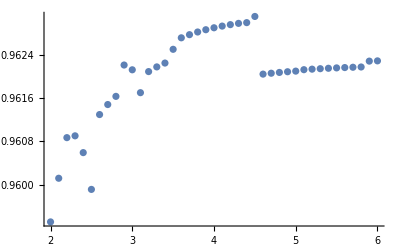

```mathematica
fitData=Table[fit=Quiet@NonlinearModelFit[fullData,{foldChange[nn,R,jj,ϵϵ]},{{βϵR,1.}},{nn,ϵϵ,R}];
{jj,fit["RSquared"]},{jj,2.,6.,0.1}];
ListPlot[fitData,PlotRange->All]
```

#### scratch

```mathematica
fitData[[First@First@Position[fitData,Max@fitData[[All,2]]]]]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

#### 5th try - Fitting together and with error

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
(*βϵR=24.1364;*)
βϵR=24.1364;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
```

```mathematica
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
(*With[{opts=opts},
Show[ListLogLogPlot[newData,Joined->True,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},opts],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]*)
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
errorData=acquire[rawData,index,"x with Error"];
weights=(Log[10,#[[2,2]]]-Log[10,#[[1,2]]])&/@Transpose@#&/@Transpose@{data[[9;;11]],errorData};
weights=Map[ErrorBar,weights,{2}];
weightedData=Riffle[#[[1]],#[[2]]]&/@Transpose@{{Log[10,#[[1]]],Log[10,#[[2]]]}&/@#&/@data[[9;;11]],weights};
weightedData=Partition[#,2]&/@weightedData;
```

```mathematica
(*errorData=acquire[rawData,index,"x with Error"];
weights=(Log[#[[2,2]]]-Log[#[[1,2]]])#[[1,2]]&/@Transpose@#&/@Transpose@{data[[9;;11]],errorData};
(*weights=Log[weights];*)
weights=Map[ErrorBar,weights,{2}]
weightedData=Riffle[#[[1]],#[[2]]]&/@Transpose@{{Log[10,#[[1]]],Log[10,#[[2]]]}&/@#&/@data[[9;;11]],weights};
weightedData=Partition[#,2]&/@weightedData;*)
```

```mathematica
plot2=Labeled[With[{opts=opts},
Show[ListPlot[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@#&/@newData,Joined->True(*,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}]*),FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LinTicks[0,4,TickLengthScale->2]/.(str_String/;str=!=""):>Superscript["10",str],LinTicks[-4,0,TickLengthScale->2]/.(str_String/;str=!=""):>Superscript["10",str]},opts],ErrorListPlot[weightedData,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
],bLabel,{{Top,Left}}]
```

-Graphics-B

#### Results of fitting ⅇ^-βϵ_R altogether with and without error

```mathematica
Grid[{{plot1,plot2}}]
```

-Graphics-A | -Graphics-B

### scratch

#### scra

```mathematica
LinTicks[0,4,TickLengthScale->2]
```

```mathematica
LinTicks[-4,0,TickLengthScale->2]/.(str_String/;str=!=""):>Superscript["10",str]
```

```mathematica
{{-4.,("10")^("-4"),{0.02,0},{}},{-3.,("10")^("-3"),{0.02,0},{}},{-2.,("10")^("-2"),{0.02,0},{}},{-1.,("10")^("-1"),{0.02,0},{}},{0.,("10")^("0"),{0.02,0},{}},{-3.8,"",{0.01,0},{}},{-3.6,"",{0.01,0},{}},{-3.4,"",{0.01,0},{}},{-3.2,"",{0.01,0},{}},{-2.8,"",{0.01,0},{}},{-2.6,"",{0.01,0},{}},{-2.4,"",{0.01,0},{}},{-2.2,"",{0.01,0},{}},{-1.8,"",{0.01,0},{}},{-1.6,"",{0.01,0},{}},{-1.4,"",{0.01,0},{}},{-1.2,"",{0.01,0},{}},{-0.8,"",{0.01,0},{}},{-0.6,"",{0.01,0},{}},{-0.3999999999999999,"",{0.01,0},{}},{-0.19999999999999996,"",{0.01,0},{}}}
```

```mathematica
{{-4.,("10")^("-4"),{0.02,0},{}},{-3.,("10")^("-3"),{0.02,0},{}},{-2.,("10")^("-2"),{0.02,0},{}},{-1.,("10")^("-1"),{0.02,0},{}},{0.,("10")^("0"),{0.02,0},{}},{-3.8,("10")^(""),{0.01,0},{}},{-3.6,("10")^(""),{0.01,0},{}},{-3.4,("10")^(""),{0.01,0},{}},{-3.2,("10")^(""),{0.01,0},{}},{-2.8,("10")^(""),{0.01,0},{}},{-2.6,("10")^(""),{0.01,0},{}},{-2.4,("10")^(""),{0.01,0},{}},{-2.2,("10")^(""),{0.01,0},{}},{-1.8,("10")^(""),{0.01,0},{}},{-1.6,("10")^(""),{0.01,0},{}},{-1.4,("10")^(""),{0.01,0},{}},{-1.2,("10")^(""),{0.01,0},{}},{-0.8,("10")^(""),{0.01,0},{}},{-0.6,("10")^(""),{0.01,0},{}},{-0.3999999999999999,("10")^(""),{0.01,0},{}},{-0.19999999999999996,("10")^(""),{0.01,0},{}}}
```

```mathematica
{{-4.,"-4",{0.02,0},{}},{-3.,"-3",{0.02,0},{}},{-2.,"-2",{0.02,0},{}},{-1.,"-1",{0.02,0},{}},{0.,"0",{0.02,0},{}},{-3.8,"",{0.01,0},{}},{-3.6,"",{0.01,0},{}},{-3.4,"",{0.01,0},{}},{-3.2,"",{0.01,0},{}},{-2.8,"",{0.01,0},{}},{-2.6,"",{0.01,0},{}},{-2.4,"",{0.01,0},{}},{-2.2,"",{0.01,0},{}},{-1.8,"",{0.01,0},{}},{-1.6,"",{0.01,0},{}},{-1.4,"",{0.01,0},{}},{-1.2,"",{0.01,0},{}},{-0.8,"",{0.01,0},{}},{-0.6,"",{0.01,0},{}},{-0.3999999999999999,"",{0.01,0},{}},{-0.19999999999999996,"",{0.01,0},{}}}
```

```mathematica
LinTicks[0,3,TickLengthScale->2]
```

```mathematica
{{0.,"0.0",{0.02,0},{}},{0.5,"0.5",{0.02,0},{}},{1.,"1.0",{0.02,0},{}},{1.5,"1.5",{0.02,0},{}},{2.,"2.0",{0.02,0},{}},{2.5,"2.5",{0.02,0},{}},{3.,"3.0",{0.02,0},{}},{0.1,"",{0.01,0},{}},{0.2,"",{0.01,0},{}},{0.30000000000000004,"",{0.01,0},{}},{0.4,"",{0.01,0},{}},{0.6,"",{0.01,0},{}},{0.7,"",{0.01,0},{}},{0.8,"",{0.01,0},{}},{0.9,"",{0.01,0},{}},{1.1,"",{0.01,0},{}},{1.2,"",{0.01,0},{}},{1.3,"",{0.01,0},{}},{1.4,"",{0.01,0},{}},{1.6,"",{0.01,0},{}},{1.7,"",{0.01,0},{}},{1.8,"",{0.01,0},{}},{1.9,"",{0.01,0},{}},{2.1,"",{0.01,0},{}},{2.2,"",{0.01,0},{}},{2.3,"",{0.01,0},{}},{2.4,"",{0.01,0},{}},{2.6,"",{0.01,0},{}},{2.7,"",{0.01,0},{}},{2.8,"",{0.01,0},{}},{2.9,"",{0.01,0},{}}}
```

#### scratch

```mathematica
ErrorListPlot[weightedData,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]
```

```mathematica
ListPlot[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@#&/@data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]
```

```mathematica
ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]
```

1. Fix this plot to also show error bars (make sure to get the axes right)
2. Then send this plot together with the previous one to Rob and co, stating that Stephanie’s idea was brilliant, and using non-linear fitting we find that most of the repressors seem to be in the active state (in line with Hernan’s assumption!)

```mathematica
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

```mathematica
errorData=acquire[rawData,index,"x with Error"];
```

```mathematica
weights=(Log[#[[2,2]]]-Log[#[[1,2]]])#[[1,2]]&/@Transpose@#&/@Transpose@{data[[9;;11]],errorData};
weights=Flatten[weights];
```

```mathematica
d=Transpose@data[[9]];
fullData1=Transpose@Join[{Table[64.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[10]];
fullData2=Transpose@Join[{Table[52.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[11]];
fullData3=Transpose@Join[{Table[10.,{Length@First@d}],Table[-17.,{Length@First@d}]},d];
fullData=Flatten[{fullData1,fullData2,fullData3},1];
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,4.5}},{nn,ϵϵ,R},Weights->1/weights^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

This indicates that with error bars accounted for, even more than the βϵ_R=4.5 (gotten without considering error bars), nearly all of the repressors should be in the active state.

```mathematica
fitData=Table[fit=Quiet@NonlinearModelFit[fullData,{foldChange[nn,R,jj,ϵϵ]},{{βϵR,4.5}},{nn,ϵϵ,R},Weights->1/weights^2,VarianceEstimatorFunction->(1&)];
{jj,fit["RSquared"]},{jj,14.,20.,2}];
ListPlot[fitData,PlotRange->All]
```

#### scratch

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,7.5}},R,Weights->1/weights[[3]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R,Weights->1/weights[[2]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,2.}},R,Weights->1/weights[[1]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

#### sc

```mathematica
file="C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx";
rawData=Import[file];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
```

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
βϵR=1.;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,7.5}},R,Weights->1/weights[[3]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R,Weights->1/weights[[2]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,2.}},R,Weights->1/weights[[1]]^2,VarianceEstimatorFunction->(1&)];
fit[{"RSquared","BestFitParameters"}]
```

#### scratch

```mathematica
errorData
data[[9;;11]]
```

```mathematica
d=data[[11]];
e=errorData[[3]];
```

```mathematica
f=Transpose@{d,e}
```

```mathematica
Transpose@{data[[9;;11]],errorData}
```

```mathematica
(Log[#[[2,2]]]-Log[#[[1,2]]])#[[1,2]]&/@Transpose@#&/@Transpose@{data[[9;;11]],errorData}
```

```mathematica
(Log[#[[2,2]]]-Log[#[[1,2]]])#[[1,2]]&/@f
```

```mathematica
(Log[#[[2]][[2]]]-Log[#[[1]][[2]]])#[[1]][[2]]&/@f
```

```mathematica
(Log[e[[1,2]]]-Log[d[[1,2]]])d[[1,2]]
(Log[e[[2,2]]]-Log[d[[2,2]]])d[[2,2]]
(Log[e[[-1,2]]]-Log[d[[-1,2]]])d[[-1,2]]
```

```mathematica
d
e
```

```mathematica
e[[1,2]]
d[[1,2]]
```

```mathematica
d[[1,2]]
```

```mathematica
(Log[e[[1,2]]]-Log[d[[1,2]]])d[[1,2]]
```

```mathematica
(Log[10,e[[1,2]]]-Log[10,d[[1,2]]])Log[10.]
```

```mathematica
1/Log[10.]
```

```mathematica
Log[10.]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange[52,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange[64,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

#### scra

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx"];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];

βϵR=10.;
newData=Transpose@Table[{{10^rLog,foldChange3[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange3[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange3[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[9;;11]]],ListLogLogPlot[newData,Joined->True,PlotLegends->{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"}]]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange3[10,R,βϵR,-17.]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Log[6.464-3.57]
Log[3.57-1.971]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[10]],{foldChange3[52,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[9]],{foldChange3[64,R,βϵR,-15.3]},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

#### scratch

```mathematica
RSquared[data_,βϵR_]:=(
theory=foldChange3[10,#,βϵR,-17.]&/@data[[All,1]];
1-((data[[All,2]]-theory).(data[[All,2]]-theory))/(data[[All,2]].data[[All,2]])
)
```

```mathematica
(data[[11,All,2]]-theory)
(data[[11,All,2]])
```

```mathematica
(-0.17830718159670667)^2
0.1426^2
```

```mathematica
(data[[11,All,2]]-theory).(data[[11,All,2]]-theory)
(data[[11,All,2]]).(data[[11,All,2]])
```

```mathematica
RSquared[data[[11]],1.]
```

```mathematica
data[[11]]
```

```mathematica
data[[All,2]].data[[All,2]]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],f3[R],{βϵ},R];
fit[{"FitResiduals","RSquared"}]
```

```mathematica
Total[(#[[2]]-f3[#[[1]]])^2&/@data[[11]]]
```

```mathematica
(#[[2]]-f3[#[[1]]])^2&/@data[[11]]
```

```mathematica
1-Total[(#[[2]]-f3[#[[1]]])^2&/@data]/Total[(data[[All,2]])^2]
```

```mathematica
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
1-Total[(#[[2]]-f[#[[1]]])^2&/@data]/Total[(data[[All,2]])^2]
```

```mathematica
data={{0,1},{1,0},{3,2},{5,4}, {6,4},{7,5}};
nlm=NonlinearModelFit[data,Log[a +b x^2],{a,b},x]
nlm[{"FitResiduals","StandardizedResiduals","RSquared"}]
{(#[[2]]-f[#[[1]]])&/@data}
```

```mathematica
Clear[f]
f[x_]:=Log[a +b x^2]/.nlm["BestFitParameters"]
```

```mathematica
1-Total[(#[[2]]-f[#[[1]]])^2&/@data]/Total[(data[[All,2]])^2]
```

```mathematica
data[[All,2]]
```

#### scratch

```mathematica
f2[R]
f3[R]
```

```mathematica
f2[R_]:=If[10<0.73 R,(∑_(m=0.)^10 ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^10 ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!)),(∑_(m=0.)^(0.73 R) ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^(0.73 R) ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))]
fit=NonlinearModelFit[data[[11]],f2[R],{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
foldChange3[10,R,1.,-17.]
```

```mathematica
NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.],βϵR==1.},{{βϵR,0.}},R]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],(∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!)),{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
foldChange[10,R,βϵR,-17.]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{(∑_(m=0.)^Min[10,(1. R)/(1.+ⅇ^-βϵR)] ((4.6*^6)^-m ⅇ^(-m (-17.+Log[1./(1.+ⅇ^-βϵR)])) (10-m) Binomial[10,m] ((1. R)/(1.+ⅇ^-βϵR))!)/(-m+(1. R)/(1.+ⅇ^-βϵR))!)/(10 ∑_(m=0.)^Min[10,(1. R)/(1.+ⅇ^-βϵR)] ((4.6*^6)^-m ⅇ^(-m (-17.+Log[1./(1.+ⅇ^-βϵR)])) Binomial[10,m] ((1. R)/(1.+ⅇ^-βϵR))!)/(-m+(1. R)/(1.+ⅇ^-βϵR))!),βϵR==1.},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
data[[11]]
```

```mathematica
foldChange[10,R,1.,-17.]
```

```mathematica
Mean@data[[11,All,2]]
```

```mathematica
1-Total[(#[[2]]-f2[#[[1]]])^2&/@data[[11]]]/Total[(#[[2]]-Mean@data[[11,All,2]])^2&/@data[[11]]]
```

```mathematica
Total[(#[[2]]-Mean@data[[11,All,2]])^2&/@data[[11]]]
```

```mathematica
Total[(#[[2]]-f2[#[[1]]])^2&/@data[[11]]]
```

```mathematica
Total[(#[[2]]-f2[#[[1]]])^2&/@data[[11]]]
```

```mathematica
f2[R_]:=If[10<0.73 R,(∑_(m=0.)^10 ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^10 ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!)),(∑_(m=0.)^(0.73 R) ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^(0.73 R) ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))](∑_(m=0.)^If[0.73 R<10,0.7310585786300049 R,10] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^If[0.7310585786300049 R<10,0.7310585786300049 R,10] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))
fit=NonlinearModelFit[data[[11]],f2[R],{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
f[R_]:=(∑_(m=0.)^If[0.7310585786300049 R<10,0.7310585786300049 R,10] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^If[0.7310585786300049 R<10,0.7310585786300049 R,10] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))
```

```mathematica
fit=NonlinearModelFit[data[[11]],f[R],{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],(∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!)),{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],(∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) (10-m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!))/(10 ∑_(m=0.)^Min[10,0.7310585786300049 R] ((4.6*^6)^-m ⅇ^(17.313261687518224 m) Binomial[10,m] (0.7310585786300049 R)!)/((-m+0.7310585786300049 R)!)),{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,1.,-17.]},{βϵ},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],{foldChange[10,R,βϵR,-17.],βϵR==1.},{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
newData=Transpose@Table[{{10^rLog,foldChange[10,10^rLog,1.,-17.]}},{rLog,0,3,0.1}];
Show[ListLogLogPlot[data[[11]]],ListLogLogPlot[newData,Joined->True]]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[data[[11]],foldChange[10,R,βϵR,-17.],{{βϵR,0.}},R];
fit[{"RSquared","BestFitParameters"}]
```

#### scratch

```mathematica
With[{opts=opts},
ListLogLogPlot[data[[9;;11]],PlotRange->{{10^0,10^3.5},{10^-4.5,10^0.5}},FrameLabel->{"Repressor Copy Number","Fold-Change"},PlotStyle->colors[[9;;11]],PlotMarkers->markers[[9;;11]],AspectRatio->1,Frame->True,FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},ImageSize->Medium,FrameStyle->Black,FrameTicksStyle->Black,Prolog->{},opts]
]
```

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx"];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
newData=Transpose@Table[{foldChange[10,10^rLog,100,-17.],foldChange[52,10^rLog,100,-15.3],foldChange[64,10^rLog,100,-15.3]},{rLog,0,3,0.1}];
Show[With[{opts=opts},
ListLogLogPlot[data[[9;;11]](*,PlotRange->{{10^0,10^3.5},{10^-4.5,10^0.5}},FrameLabel->{"Repressor Copy Number","Fold-Change"},AspectRatio->1,Frame->True,FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},ImageSize->Medium,FrameStyle->Black,FrameTicksStyle->Black,Prolog->{},opts*)]
],ListLogLogPlot[newData,Joined->True,PlotLegends->{"Oid, N_s=10","O1, N_s=52","O1, N_s=64"}]]
```

```mathematica
Table[{foldChange[10,10^rLog,100,-17.],foldChange[52,10^rLog,100,-15.3],foldChange[64,10^rLog,100,-15.3]},{rLog,0,3,0.1}]
```

```mathematica
NonlinearModelFit[foldChange[10,R,100,-17.]]
```

## Stephanie’s New Idea - Calculating ⅇ^-βϵ_R including operator copy number

#### Background

Continuing with more brilliant ideas, Stephanie pointed out that the specific operator DNA sequences (especially when they are present in multiple copy numbers) can pull more repressors into the active state, so that it may be an oversimplification to assume

p_active=1/(1+ⅇ^-βϵ_R)

Instead, if we let the states of the repressor be

State | Weight
nonspecifically bound,active | 1
nonspecifically bound,inactive | ⅇ^-βϵ_R
specifically bound,active | O/N_NS ⅇ^-βϵ_DNA
specifically bound,inactive | 0

where we have assumed that the inactive repressor does not bind to DNA.

Note the fundamental issue that we are trying to tackle. Everyone agrees that p_bound is given by

p_bound=(P/N_NS ⅇ^(-βϵ_(DNA,pol)))/(1+P/N_NS ⅇ^(-βϵ_(DNA,pol))+(p_active R_tot)/N_NS ⅇ^(-βϵ_(DNA,R_active))+((1-p_active)R_tot)/N_NS ⅇ^(-βϵ_(DNA,R_inactive)))

which leads to the fold-change expression (assuming the inactive repressor does not bind DNA and the weak promoter approximation)

fold-change=1/(1+p_active R_tot/N_NS ⅇ^(-βϵ_(DNA,R_active))).

But the question we are asking now is, what is the form of p_active? Hernan originally postulated that

p_active≈1,

assuming that all repressors were active. After that, we went to the more refined form of stating

p_active=1/(1+ⅇ^-βϵ_R).

According to Rob Brewster’s data, it seems that with this form, the best fit βϵ_R≳4.5, so that Hernan’s assumption was fine. But now with Stephanie’s point about the copy number of the promoter mattering, she is bringing this bad boy into the realm of

p_active=(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R),

which makes everything much more complicated. This form, if correct, implies that Hernan actually measured

ⅇ^(-βϵ_(DNA,R_active)^Hernan)≡(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R)ⅇ^(-βϵ_(DNA,R_active))

This can be solved for the new version of ⅇ^(-βϵ_(DNA,R_active)) in terms of ⅇ^(-βϵ_(DNA,R_active)^Hernan) as

```mathematica
sol=FullSimplify[Solve[E^-βϵDNAHernan==(1+1/Nns E^-βϵDNA)/(1+1/Nns E^-βϵDNA+E^-βϵR)E^-βϵDNA,βϵDNA]/.C[1]->0,βϵDNA>0];
(* Only second solution is positive *)
sol1=Last@FullSimplify[sol]
sol2=Last@FullSimplify[E^-βϵDNA/.sol]
(*sol2/.{Nns->4.6 10^6,βϵDNAHernan->-13.7,βϵR->4.5}*)
```

{βϵDNA→Log[(ⅇ^βϵR (-1+ⅇ^βϵDNAHernan Nns)+ⅇ^(βϵR/2) √(ⅇ^βϵR+2 ⅇ^βϵDNAHernan (2+ⅇ^βϵR) Nns+ⅇ^(2 βϵDNAHernan+βϵR) Nns^2))/(2 (1+ⅇ^βϵR) Nns)]}

(2 (1+ⅇ^βϵR) Nns)/(ⅇ^βϵR (-1+ⅇ^βϵDNAHernan Nns)+ⅇ^(βϵR/2) √(ⅇ^βϵR+2 ⅇ^βϵDNAHernan (2+ⅇ^βϵR) Nns+ⅇ^(2 βϵDNAHernan+βϵR) Nns^2))

#### Data Fitting

The basic idea is that when you have multiple promoters with copy number N>1, the fold-change equation allows you to actually fit the ⅇ^-βϵ_R parameter, since it shifts the resulting fold-change curve to the right as ϵ_R decreases.

fold-change=(∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA)(N-m))/(N∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA))

R_eff=p_active R_tot

p_active=(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R),

Relating this to Hernan’s data where O=1,

ⅇ^(-βϵ_(DNA,R_active)^Hernan)≡(1+1/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+1/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R)ⅇ^(-βϵ_(DNA,R_active))

### Code

#### Plotting the form of fold-change (same as in preivous set of notes)

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=E(*N[E]*)},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
(* Plot has a hard time with this function, because the Min naturally makes the plot bumpy, which is hard to calculate precisely *)
(*LogLogPlot[{foldChange[10.,r,-2.,-17.],foldChange[10.,r,2.,-17.]},{r,10^0,10^3},PerformanceGoal->"Speed"]*)
```

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
relabel@ListLogLogPlot[data,Joined->True,PlotLegends->("βϵ_R="<>ToString@#&/@βϵValues),FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),opts]
```

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
leg=LineLegend[ColorData[97]/@Range@Length@βϵValues,font[#,10]&/@("βϵ_R="<>ToString@#&/@βϵValues),Spacings->{0.5,0.2}];
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
ListLogLogPlot[data,Joined->True,PlotLegends->leg,FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^3,TickLengthScale->2],LogTicks[10^-4,10^0,TickLengthScale->2]},opts]
```

#### 1st try - Fitting together and without error

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx"];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
```

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{nNS=4.6 10^6.},
With[{βϵDNA=Log[1/(2 (1+ⅇ^βϵR) nNS)(ⅇ^βϵR (-1+ⅇ^βϵHernanDNA nNS)+ⅇ^(βϵR/2) √(ⅇ^βϵR+2 ⅇ^βϵHernanDNA (2+ⅇ^βϵR) nNS+ⅇ^(2 βϵHernanDNA+βϵR) nNS^2))]},
With[{rEff=(1.+n/nNS E^-βϵDNA)/(1.+n/nNS E^-βϵDNA+E^-βϵR)r,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
]
]
```

```mathematica
βϵR=4.525127;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
```

```mathematica
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
plot1=Labeled[With[{opts=opts},
Show[ListLogLogPlot[newData,Joined->True,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},opts],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
],aLabel,{{Top,Left}}]
```

```mathematica
d=Transpose@data[[9]];
fullData1=Transpose@Join[{Table[64.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[10]];
fullData2=Transpose@Join[{Table[52.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[11]];
fullData3=Transpose@Join[{Table[10.,{Length@First@d}],Table[-17.,{Length@First@d}]},d];
fullData=Flatten[{fullData1,fullData2,fullData3},1];
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,4.5}},{nn,ϵϵ,R}];
fit[{"RSquared","BestFitParameters"}]
```

But what if we look at other starting values of βϵR?

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,-0.1}},{nn,ϵϵ,R}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
fitData=Table[fit=Quiet@NonlinearModelFit[fullData,{foldChange[nn,R,jj,ϵϵ]},{{βϵR,1.}},{nn,ϵϵ,R}];
{jj,fit["RSquared"]},{jj,-5.,5.,1.0}];
ListPlot[fitData,PlotRange->All]
```

#### Results

```mathematica
file="C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx";
rawData=Import[file];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
```

```mathematica
βϵR=5.0;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
plot1=With[{opts=opts},
Show[ListLogLogPlot[newData,Joined->True,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],PlotLabel->"βϵ_R="<>ToString[βϵR],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},opts],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

```mathematica
βϵR=0.0;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
plot2=With[{opts=opts},
Show[ListLogLogPlot[newData,Joined->True,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],PlotLabel->"βϵ_R="<>ToString[βϵR],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},opts],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

```mathematica
Grid[{{plot1,plot2}}]
```

## Stephanie’s New New Idea - Calculating ⅇ^-βϵ_R using operator copy number but using simple form for Hernan’s energy

#### Background

Continuing with more brilliant ideas, Stephanie pointed out that the specific operator DNA sequences (especially when they are present in multiple copy numbers) can pull more repressors into the active state, so that it may be an oversimplification to assume

p_active=1/(1+ⅇ^-βϵ_R)

Instead, if we let the states of the repressor be

State | Weight
nonspecifically bound,active | 1
nonspecifically bound,inactive | ⅇ^-βϵ_R
specifically bound,active | O/N_NS ⅇ^-βϵ_DNA
specifically bound,inactive | 0

where we have assumed that the inactive repressor does not bind to DNA.

Note the fundamental issue that we are trying to tackle. Everyone agrees that p_bound is given by

p_bound=(P/N_NS ⅇ^(-βϵ_(DNA,pol)))/(1+P/N_NS ⅇ^(-βϵ_(DNA,pol))+(p_active R_tot)/N_NS ⅇ^(-βϵ_(DNA,R_active))+((1-p_active)R_tot)/N_NS ⅇ^(-βϵ_(DNA,R_inactive)))

which leads to the fold-change expression (assuming the inactive repressor does not bind DNA and the weak promoter approximation)

fold-change=1/(1+p_active R_tot/N_NS ⅇ^(-βϵ_(DNA,R_active))).

But the question we are asking now is, what is the form of p_active? Hernan originally postulated that

p_active≈1,

assuming that all repressors were active. After that, we went to the more refined form of stating

p_active=1/(1+ⅇ^-βϵ_R).

According to Rob Brewster’s data, it seems that with this form, the best fit βϵ_R≳4.5, so that Hernan’s assumption was fine. But now with Stephanie’s point about the copy number of the promoter mattering, she is bringing this bad boy into the realm of

p_active=(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R),

which makes everything much more complicated. Note, however, that this form is only correct when the number of operators O≫R. For example, in the case of Hernan’s experiments where there is only 1 operator, we still have the typical form (since even if the operator does influence one of the repressors, it is only 1 among R)

ⅇ^(-βϵ_(DNA,R_active)^Hernan)≡1/(1+ⅇ^-βϵ_R)ⅇ^(-βϵ_(DNA,R_active))

```mathematica
sol=FullSimplify[Solve[E^-βϵDNAHernan==1/(1+E^-βϵR)E^-βϵDNA,βϵDNA]/.C[1]->0,βϵDNA>0];
(* Only second solution is positive *)
sol1=Last@FullSimplify[sol]
sol2=Last@FullSimplify[E^-βϵDNA/.sol]
(*sol2/.{Nns->4.6 10^6,βϵDNAHernan->-13.7,βϵR->4.5}*)
```

{βϵDNA→Log[ⅇ^(βϵDNAHernan+βϵR)/(1+ⅇ^βϵR)]}

ⅇ^(-βϵDNAHernan-βϵR) (1+ⅇ^βϵR)

#### Data Fitting

The basic idea is that when you have multiple promoters with copy number N>1, the fold-change equation allows you to actually fit the ⅇ^-βϵ_R parameter, since it shifts the resulting fold-change curve to the right as ϵ_R decreases.

fold-change=(∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA)(N-m))/(N∑_(m=0)^Min[N,R_eff] (R_eff!)/((N_ns)^m(R_eff-m)!)(N
m)ⅇ^(-m βϵ_DNA))

R_eff=p_active R_tot

p_active=(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active)))/(1+O/N_NS ⅇ^(-βϵ_(DNA,R_active))+ⅇ^-βϵ_R),

Relating this to Hernan’s data (which is not the case O=1 because the above form assumes O≫R),

ⅇ^(-βϵ_(DNA,R_active)^Hernan)≡1/(1+ⅇ^-βϵ_R)ⅇ^(-βϵ_(DNA,R_active))

### Code

#### Plotting the form of fold-change (same as in preivous set of notes)

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{rEff=1./(1.+E^-βϵR)r,βϵDNA=βϵHernanDNA+Log[1./(1.+E^-βϵR)],nNS=4.6 10^6.,e=E(*N[E]*)},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
```

```mathematica
(* Plot has a hard time with this function, because the Min naturally makes the plot bumpy, which is hard to calculate precisely *)
(*LogLogPlot[{foldChange[10.,r,-2.,-17.],foldChange[10.,r,2.,-17.]},{r,10^0,10^3},PerformanceGoal->"Speed"]*)
```

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
relabel@ListLogLogPlot[data,Joined->True,PlotLegends->("βϵ_R="<>ToString@#&/@βϵValues),FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),opts]
```

-Graphics-

```mathematica
βϵValues={10,2,1,0,-1,-2,-3,-4,-5,-10};
leg=LineLegend[ColorData[97]/@Range@Length@βϵValues,font[#,10]&/@("βϵ_R="<>ToString@#&/@βϵValues),Spacings->{0.5,0.2}];
data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
ListLogLogPlot[data,Joined->True,PlotLegends->leg,FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^3,TickLengthScale->2],LogTicks[10^-4,10^0,TickLengthScale->2]},opts]
```

-Graphics-

#### 1st try - Fitting together and without error

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx"];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
```

```mathematica
foldChange[n_,r_,βϵR_,βϵHernanDNA_]:=With[{nNS=4.6 10^6.},
With[{βϵDNA=Log[ⅇ^(βϵHernanDNA+βϵR)/(1+ⅇ^βϵR)]},
With[{rEff=(1.+n/nNS E^-βϵDNA)/(1.+n/nNS E^-βϵDNA+E^-βϵR)r,e=N[E]},
Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA)(n-m),{m,0.,Min[n,rEff]}]/(n Sum[(rEff!)/(nNS^m(rEff-m)!)Binomial[n,m] e^(-m βϵDNA),{m,0.,Min[n,rEff]}])
]
]
]
```

```mathematica
Clear[βϵR]
plot[βϵR_]:=
(
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[52,10^rLog,βϵR,-15.3]},{10^rLog,foldChange[10,10^rLog,βϵR,-17.]}},{rLog,0,3,0.1}];
labels=font/@{"O1, N_s=64","O1, N_s=52","Oid, N_s=10"};
leg=PointLegend[ColorData[97]/@Range@3,labels,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.4}];
plot1=With[{opts=opts},
Show[ListLogLogPlot[newData,Joined->True,PlotLegends->Placed[leg,{Scaled[{0.05,0.3}], {0, 0.5}}],FrameLabel->(font[#,10]&/@{"Repressor Copy Number","Fold-Change"}),FrameTicks->{LogTicks[10^0,10^4,TickLengthScale->2],LogTicks[10^-5,10^1,TickLengthScale->2]},PlotLabel->"βϵ_R="<>ToString[βϵR],opts],ListLogLogPlot[data[[9;;11]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
)
```

```mathematica
Grid[{{plot[0],plot[1.5]},{plot[4.5],plot[6]}}(*,Spacings->-1*)]
```

-Graphics-

```mathematica
d=Transpose@data[[9]];
fullData1=Transpose@Join[{Table[64.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[10]];
fullData2=Transpose@Join[{Table[52.,{Length@First@d}],Table[-15.3,{Length@First@d}]},d];
d=Transpose@data[[11]];
fullData3=Transpose@Join[{Table[10.,{Length@First@d}],Table[-17.,{Length@First@d}]},d];
fullData=Flatten[{fullData1,fullData2,fullData3},1];
```

```mathematica
Clear[βϵR]
fitResults=Table[
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ],βϵR==jj},{{βϵR,4.5}},{nn,ϵϵ,R}];
{jj,fit["RSquared"]}
,{jj,{-4,-2,-1,0,1.5,4.5,6}}]
```

{{-4,0.961822},{-2,0.962265},{-1,0.962523},{0,0.962006},{1.5,0.962356},{4.5,0.961905},{6,0.961902}}

```mathematica
Clear[βϵR]
fitResults=Table[
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ],βϵR==jj},{{βϵR,4.5}},{nn,ϵϵ,R}];
{jj,fit["RSquared"]}
,{jj,0,5,1.0}]
```

{{0.,0.962006},{1.,0.962222},{2.,0.962025},{3.,0.961915},{4.,0.961907},{5.,0.961903}}

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,4.5}},{nn,ϵϵ,R}];
fit[{"RSquared","BestFitParameters"}]
```

{0.962357,{βϵR→1.65168}}

But what if we look at other starting values of βϵR?

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullData,{foldChange[nn,R,βϵR,ϵϵ]},{{βϵR,-0.1}},{nn,ϵϵ,R}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
fitData=Table[fit=Quiet@NonlinearModelFit[fullData,{foldChange[nn,R,jj,ϵϵ]},{{βϵR,1.}},{nn,ϵϵ,R}];
{jj,fit["RSquared"]},{jj,-5.,5.,1.0}];
ListPlot[fitData,PlotRange->All]
```

#### Conclusion

It seems that any ϵ_R value seems to work equally well. I say it is time to simply judiciously make an assumption (and I vote for the assumption that Hernan was correct!) and simplify the fold-change to

1/(1+((1+c/K_A)^2(1+ⅇ^-βϵ_R))/((1+c/K_A)^2+(ⅇ^-βϵ_R(1+c/K_I))^2)R/N_NS ⅇ^(-βϵ_DNA^Hernan))≈1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^-βϵ_R c^2)/K_I^2)R/N_NS ⅇ^(-βϵ_DNA^Hernan))

## Stephanie FACS Data

#### Importing Data

```mathematica
rawData=Import["C:\\Users\\Tal\\Dropbox\\Research\\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\\Discussions\\2016-06-18 Stephanie Data - O2 HG104 and 1027.xlsx"];
```

```mathematica
index=1;
data=acquire[rawData,index,"[IPTG]"];
```

```mathematica
SetAttributes[convertString,{Listable}];
convertString[""]:=""
convertString[str_String]:=Module[{unit},
Switch[StringTake[str,{-2,-1}],"nM",10^-9.,"uM",10^-6.,"mM",10^-3.]*ToExpression@StringTrim@StringTake[str,{1,-3}]
]
convertString[num_Real]:=num
```

```mathematica
data2=DeleteCases[convertString@data,{_,""},{2}];
(* Partition off individuals strains *)
{HG104,RBS1027}={Flatten[data2[[1;;3]],1],Flatten[data2[[4;;6]],1]};
```

```mathematica
leg=PointLegend[ColorData[97]/@{1,2},{"HG 104","RBS 1027"}];
ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]]
```

#### Fitting Data - Trying βϵ_R=5 from Stephanie’s brilliant idea

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullRData,fitFunction2[R]/.βϵR->5./.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
Clear[βϵR]
fit=NonlinearModelFit[fullRData,fitFunction2[R]/.βϵR->4.5/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.βϵR->4.5/.fit["BestFitParameters"]);
parameters2=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Fitting Data with n=2 - Using only RBS 1027 from last time to predict WT - seems to work well

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
plot1=Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Evaluate[{fitFunction2[11],fitFunction2[130]}];
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=2, Using RBS 1027 to fit HG 104",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@With[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},{KA,KI,βϵR}];
parameters1=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Fitting Data - Fitting all data with n=2

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction2[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot2=Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Normal@fit/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"Fitting All Data",ImageSize->Medium],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.fit["BestFitParameters"]);
parameters2=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Fitting Data - Fitting all data with n=2 - Adjusting βϵR to be reasonable

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction2[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot2=Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=fitFunction2[R]/.{KA->E^KAlog,KI->E^KIlog}/.βϵR->-4./.fit["BestFitParameters"]/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=2, Fitting All Data",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.βϵR->-4./.fit["BestFitParameters"]);
parameters2=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Using RBS 1027 to predict HG 104 with n=4 (adjusting the βϵR parameter value)

```mathematica
Clear[c,fitFunction4]
(* Fold change formula with square exponents *)
fitFunction4[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^4(1+ⅇ^-βϵR))/((1+c/KA)^4+ⅇ^-βϵR(1+c/KI)^4)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fit=NonlinearModelFit[RBS1027,fitFunction4[R]/.{R->130,KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},c];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot3=(
plots=fitFunction4[R]/.{KA->E^KAlog,KI->E^KIlog}/.βϵR->-4./.fit["BestFitParameters"]/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=4, Using RBS 1027 to fit HG 104",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
)
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.βϵR->-4./.fit["BestFitParameters"]);
parameters3=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Trying fitting all data with n=4

```mathematica
Clear[c,fitFunction4]
(* Fold change formula with square exponents *)
fitFunction4[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^4(1+ⅇ^-βϵR))/((1+c/KA)^4+ⅇ^-βϵR(1+c/KI)^4)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction4[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot4=(
plots=Normal@fit/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"Fitting All Data",ImageSize->Medium],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
)
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.fit["BestFitParameters"]);
parameters4=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Trying fitting all data with n=4 (adjusting the βϵR parameter value)

```mathematica
Clear[c,fitFunction4]
(* Fold change formula with square exponents *)
fitFunction4[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^4(1+ⅇ^-βϵR))/((1+c/KA)^4+ⅇ^-βϵR(1+c/KI)^4)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction4[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot4=(
plots=fitFunction4[R]/.{KA->E^KAlog,KI->E^KIlog}/.βϵR->-4./.fit["BestFitParameters"]/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=4, Fitting All Data",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
)
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.βϵR->-4./.fit["BestFitParameters"]);
parameters4=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### Results of above sections

```mathematica
Grid[{{plot1,plot2},{parameters1,parameters2}}]
Grid[{{plot3,plot4},{parameters3,parameters4}}]
```

#### n=2 with Mitch data

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
plot5=(
plots={fitFunction2[11],fitFunction2[130]}/.{KA->1.5 10^-5,KI->1.2 10^-6,βϵR->-Log[1.1]};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=2, Mitch Values",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
)
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({1.5 10^-5,1.2 10^-6,-Log[1.1]});
parameters5=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### n=4 with Mitch data

```mathematica
plot6=(
plots={fitFunction4[11],fitFunction4[130]}/.{KA->1.5 10^-5,KI->1.2 10^-6,βϵR->-Log[1.1]};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=4, Mitch Values",ImageSize->size],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
)
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({1.5 10^-5,1.2 10^-6,-Log[1.1]});
parameters6=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

```mathematica
Grid[{{plot5,plot6},{parameters5,parameters6}}]
```

#### Trying to fit n=2 with βϵ_R=10

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction2[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9,βϵR=5.},1/(1+((1+c/KA)^2(1+ⅇ^-βϵR))/((1+c/KA)^2+ⅇ^-βϵR(1+c/KI)^2)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction2[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]}(*,{βϵR,-Log[55.]}*)},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot2=Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Normal@fit/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"n=2, βϵ_R=10, Fitting All Data",ImageSize->Medium],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=With[{βϵR=5.},scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.fit["BestFitParameters"])];
parameters2=TextGrid[{{Row[{Subscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Subscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

```mathematica
Column[{plot2,parameters2},Alignment->Center]
```

#### Moving along βϵ_R space

```mathematica
Clear[c,fitFunction3]
(* Fold change formula with square exponents *)
fitFunction3[R_,βϵR_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1./(1.+((1.+c/KA)^2.(1.+ⅇ^-βϵR))/((1.+c/KA)^2.+ⅇ^-βϵR(1.+c/KI)^2.)(2.R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
βϵMin=-20.;βϵMax=20.;βϵInc=1.;
parameters=Table[
fit=NonlinearModelFit[fullRData,fitFunction3[R,βϵ]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]}},{R,c}];
{βϵ,E^KAlog,E^KIlog}/.fit["BestFitParameters"]
,{βϵ,βϵMin,βϵMax,βϵInc}];
```

```mathematica
plots=fitFunction3[R,#[[1]]]/.{KA->#[[2]],KI->#[[3]]}/.{{R->11},{R->130}}&/@parameters[[1;;-1;;4]];
```

```mathematica
plot1=With[{opts=opts},
Labeled[Show[LogLinearPlot[Evaluate@Flatten[Transpose@plots],{c,10^-9,10^-2}(*,PlotLabel->"n=2, Different βϵ_R Values"*),PlotStyle->Join[ColorData[97][1]&/@Range@Length@plots,ColorData[97][2]&/@Range@Length@plots],Axes->False,PlotRangePadding->Automatic,FrameLabel->{"[IPTG]","fold-change"},opts],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All],aLabel,{{Top,Left}}]
]
```

```mathematica
plot2=Labeled[ListLogPlot[{parameters[[All,{1,2}]],parameters[[All,{1,3}]](*,Transpose@{parameters[[All,1]],E^(-parameters[[All,1]])/parameters[[All,3]]^2}*)},PlotStyle->ColorData[97]/@{3,4,5},PlotLegends->Placed[{"K_A","K_I","K_Iⅇ^βϵ_R"},Scaled[{{0.2,0.3},{0.5,0.5}}]],FrameLabel->{"βϵ","Best-fit Parameters"},Axes->False,opts],bLabel,{{Top,Left}}]
```

```mathematica
grid=Grid[{{plot1,plot2}}]
```

```mathematica
plot3=ListLogPlot[{parameters[[All,{1,3}]],Transpose@{parameters[[All,1]],E^(-parameters[[All,1]])/parameters[[All,3]]^2}},PlotStyle->ColorData[97]/@{3,4,5},PlotLegends->Placed[{"K_I","K_Iⅇ^βϵ_R"},Scaled[{{0.2,0.4},{0.5,0.5}}]],FrameLabel->{"βϵ","Best-fit Parameters"},Axes->False,opts]
```

```mathematica
Export["C:\\Users\\Tal\\Dropbox\\Research\\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\\Discussions\\2016-06-06 Counting Plasmids\\fittingParameters.pdf",grid];
```

```mathematica
Export["C:\\Users\\Tal\\Dropbox\\Research\\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\\Discussions\\2016-06-06 Counting Plasmids\\fittingParameters2.pdf",plot3];
```

#### Summary of ⅇ^-βϵ_R≪1

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(c/((K̃)_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

for parameters K_A and (K̃)_I≡K_I/ⅇ^(-βϵ_R/2)

The parameters from fitting will satisfy these two conditions:

(K̃)_I≈[EC_50]/(1+r)^(1/2)

K_A≈[EC_50]((dynamicRange-1/(1+r))/(1-dynamicRange))^(1/2)

#### Limit ⅇ^-βϵ_R≪1

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^-βϵ_R(1+c/K_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

fold-change≈1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^-βϵ_R(c/K_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))≡1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(c/((K̃)_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

Thus we are really fitting the parameters K_A and (K̃)_I=K_I/ⅇ^(-βϵ_R/2)

```mathematica
ListLogPlot[{parameters[[All,{1,3}]],Transpose@{parameters[[All,1]],E^(-parameters[[All,1]])/parameters[[All,3]]^2}}]
```

To quantify the exact values of K_A and ⅇ^-βϵ_R/K_I^2, let’s find [EC_50],

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^-βϵ_R(c/K_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(c/((K̃)_I))^2)R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

```mathematica
fc=1/(1+(1+c/KA)^2/((1+c/KA)^2+c^2/KIeff^2)r);
fcMin=Limit[fc,c->0]
fcMax=Limit[fc,c->∞]
```

```mathematica
FullSimplify@Solve[dynamicRange==(KA^2+KIeff^2)/(KA^2+KIeff^2 (1+r)),KA]
```

```mathematica
FullSimplify@Solve[dynamicRange==(KRatio^2+1)/(KRatio^2+(1+r)),KRatio]
```

K_A/((K̃)_I)=(√(dynamicRange (1+r)-1))/(√(1-dynamicRange))

```mathematica
val[KRatio/.FullSimplify@Solve[dynamicRange==(KRatio^2+1)/(KRatio^2+(1+r)),KRatio]/.dynamicRange->0.7]
```

```mathematica
parameters[[-1]]
```

```mathematica
val[x_]:=x/.{KA->parameters[[-1,2]],KIeff->parameters[[-1,3]]/E^(-parameters[[-1,1]]/2),r->11/(4.6 10^6)E^13.9}
```

```mathematica
val[{(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2+2 KIeff^2 (1+r))))/(KA^2+KIeff^2 (1+r)),(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2)))/(KA^2+KIeff^2 (1+r)),(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2)))/KA^2,KIeff(KIeff/KA (1+r)+√(1+r)),KIeff(KIeff/KA(1+r)+(1+r)^(1/2)),KIeff(1+r)^(1/2)(KIeff/KA(1+r)^(1/2)+1)}]
```

```mathematica
val[{KA,KIeff,r}]
```

```mathematica
val[{KIeff/KA(1+r)^(1/2)+1,KIeff/KA(1+r)^(1/2),1}]
```

```mathematica
val[r]
```

(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2+2 KIeff^2 (1+r))))/(KA^2+KIeff^2 (1+r))≈(K_A (K̃)_I^2 (1+r)+K_A^2(K̃)_I √(1+r))/K_A^2

(K̃)_I(((K̃)_I)/K_A (1+r)+√(1+r))≈(K̃)_I √(1+r)

```mathematica
FullSimplify@Solve[1/2==Simplify[(fc-fcMin)/(fcMax-fcMin)],c]
```

#### Limit ⅇ^-βϵ_R≫1

fold-change≈1/(1+(1+c/K_A)^2/(1+c/((K̃)_I))^2 R/N_ns ⅇ^(-βϵ_O2^(Hernan)))

```mathematica
fc=1/(1+(1+c/KA)^2/(1+c/KI)^2 r);
fcMin=Limit[fc,c->0]
fcMax=Limit[fc,c->∞]
```

```mathematica
FullSimplify@Solve[dynamicRange==KRatio^2/(KRatio^2+r),KRatio]
```

K_A/K_I=(√(dynamicRange  r))/(√(1-dynamicRange))

```mathematica
val2[x_]:=x/.{KA->parameters[[1,2]],KI->parameters[[1,3]],r->11/(4.6 10^6)E^13.9}
```

```mathematica
val2[{10^-5/((2+r)^(1/2)-1),(10^-5 r^(1/2))/((2+r)^(1/2)-1)(0.8/(1-0.8))}]
```

```mathematica
{KA->parameters[[1,2]],KI->parameters[[1,3]],r->11/(4.6 10^6)E^13.9}
```

```mathematica
val[{(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2+2 KIeff^2 (1+r))))/(KA^2+KIeff^2 (1+r)),(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2)))/(KA^2+KIeff^2 (1+r)),(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2)))/KA^2,KIeff(KIeff/KA (1+r)+√(1+r)),KIeff(KIeff/KA(1+r)+(1+r)^(1/2)),KIeff(1+r)^(1/2)(KIeff/KA(1+r)^(1/2)+1)}]
```

```mathematica
val[{KA,KIeff,r}]
```

```mathematica
val[{KIeff/KA(1+r)^(1/2)+1,KIeff/KA(1+r)^(1/2),1}]
```

```mathematica
val[r]
```

(KA KIeff^2 (1+r)+√(KA^2 KIeff^2 (1+r) (KA^2+2 KIeff^2 (1+r))))/(KA^2+KIeff^2 (1+r))≈(K_A (K̃)_I^2 (1+r)+K_A^2(K̃)_I √(1+r))/K_A^2

(K̃)_I(((K̃)_I)/K_A (1+r)+√(1+r))≈(K̃)_I √(1+r)

```mathematica
FullSimplify@Solve[1/2==Simplify[(fc-fcMin)/(fcMax-fcMin)],c]
```

(-KA  KI + KI KA √( (2+r)))/(KA+KI)

```mathematica
val[{(-KA (KA-KI) KI (KA-KI r)+√(KA^2 KI^2 (KI^2 r+KA^2 (2+r)) (KA^2+KI^2 (1+2 r))))/((KA+KI) (KA^2+KI^2 r)),KA KI ((-1+√(2+r))/(KA+KI)),KI (-1+√(2+r))}]
```

```mathematica
val[r]
```

```mathematica
val[c/.FullSimplify@Solve[1/2==Simplify[(fc-fcMin)/(fcMax-fcMin)],c]]
```

### scratch

#### sc

```mathematica
Clear[c,fitFunction2]
(* Fold change formula with square exponents *)
fitFunction4[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9},1/(1+((1+c/KA)^4(1+ⅇ^-βϵR))/((1+c/KA)^4+ⅇ^-βϵR(1+c/KI)^4)(2R)/Nns ⅇ^-βϵO2)];
```

```mathematica
fullRData=Join[Transpose@Prepend[Transpose[#],Table[11,{Length@#}]]&@HG104,Transpose@Prepend[Transpose[#],Table[130,{Length@#}]]&@RBS1027];
```

```mathematica
fit=NonlinearModelFit[fullRData,fitFunction4[R]/.{KA->E^KAlog,KI->E^KIlog},{{KAlog,Log[1.5 10^-4]},{KIlog,Log[6.2 10^-6]},{βϵR,-Log[55.]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
plot4=Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Normal@fit/.{{R->11},{R->130}};
Show[LogLinearPlot[plots,{c,10^-9,10^-2},PlotLabel->"Fitting All Data",ImageSize->Medium],ListLogLinearPlot[{HG104,RBS1027},PlotStyle->ColorData[97]/@{1,2},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotLegends->Placed[{"HG 104","RBS 1027"},Scaled[{{0.25,0.65},{0.5,0.5}}]]],PlotRange->All]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,βϵR}/.fit["BestFitParameters"]);
parameters2=TextGrid[{{Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Superscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],font@"βϵ"},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

#### sc

```mathematica
With[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},Plot[{fitFunction2[11],fitFunction2[130]},{c,10^-9,10^-3}]]
```

```mathematica
With[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},Evaluate[{fitFunction2[11],fitFunction2[130]}]]
```

```mathematica
Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Evaluate[{fitFunction2[11],fitFunction2[130]}]
]
```

```mathematica
Block[{KA=1.5 10^-4,KI=6.2 10^-6,βϵR=-Log[55.]},
plots=Evaluate[{fitFunction2[11],fitFunction2[130]}];
LogLinearPlot[plots,{c,10^-9,10^-3}]
]
```

```mathematica
plots
```

## Griffin’s Microscopy Data

#### Background

Raw data:

RBS 1027 data from 2016-06-10

WT data from 2016-06-06

```mathematica
-Graphics--Graphics-
```

Fitting data to an O2 repressor binding region (ϵ_(DNA,O2)^(Hernan)=-13.9 k_B T) assuming RBS 1027 has 130±20 repressors. Fold-change takes the form

fold-change=1/(1+((1+c/K_A)^2(1+ⅇ^(-β ϵ_R)))/((1+c/K_A)^2+(ⅇ^(-β ϵ_R)(1+c/K_I))^2)(2R)/N_ns ⅇ^(-β ϵ_DNA^(Hernan))).

### 2016-06-11 Fitting RBS 1027 alone

#### Fitting

```mathematica
fit=NonlinearModelFit[RBS1027data,With[{R=130,Nns=4.6 10^6,βϵO2=-13.9},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],{{KAlog,Log[1.5 10^-5]},{KIlog,Log[1.2 10^-6]},{βϵR,-Log[1.1]}},c];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
With[{opts=opts},
Show[relabel@LogLinearPlot[Normal@fit,{c,10^-8,10^-2},FrameLabel->font/@{"[inducer] (M)","fold-change"},opts],ListLogLinearPlot[RBS1027data,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

```mathematica
{E^KAlog,E^KIlog,E^-βϵR}/.fit["BestFitParameters"]
```

```mathematica
fit["BestFitParameters"]
```

#### Manipulate to see if we can un-crazify the parameters

It seems that you can wiggle ϵ_R way down without affecting the resulting fold-change form at all! That is a very bad sign for our hope of really nailing down this parameter.

```mathematica
Manipulate[
With[{opts=opts},
Show[relabel@LogLinearPlot[With[{R=130,Nns=4.6 10^6,βϵO2=-13.9},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],{c,10^-8,10^-2},FrameLabel->font/@{"[inducer] (M)","fold-change"},PlotRange->{Automatic,{0,1}},opts],ListLogLinearPlot[RBS1027data,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
,{{KAlog,-8.803200138715422},-20,20},{{KIlog,-11.992524472359802},-20,20},{{βϵR,-35.99141676936049},-36,5}]
```

```mathematica
fit=NonlinearModelFit[RBS1027data,With[{R=130,Nns=4.6 10^6,βϵO2=-13.9,βϵR=-4.},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],{{KAlog,Log[1.5 10^-5]},{KIlog,Log[1.2 10^-6]}(*,{βϵR,-Log[1.1]}*)},c];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
{E^KAlog,E^KIlog,E^-βϵR}/.{KAlog->-8.805296871016626,KIlog->-12.003247472604826}
```

```mathematica
With[{opts=opts},
Show[relabel@LogLinearPlot[With[{R=130,Nns=4.6 10^6,βϵO2=-13.9,βϵR=-4.,KAlog=-8.805296871016626,KIlog=-12.003247472604826},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],{c,10^-8,10^-2},FrameLabel->font/@{"[inducer] (M)","fold-change"},PlotRange->{Automatic,{0,1}},PlotLabel->"RBS 1027",opts],ListLogLinearPlot[RBS1027data,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

### 2016-06-15 Fitting RBS 1027 and WT

```mathematica
-Graphics--Graphics-
```

```mathematica
combinedData=Join[
Prepend[#,130]&/@RBS1027data,
Prepend[#,11]&/@WTdata
];
```

```mathematica
fit=NonlinearModelFit[combinedData,With[{(*R=130,*)Nns=4.6 10^6,βϵO2=-13.9},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],{{KAlog,Log[1.5 10^-5]},{KIlog,Log[1.2 10^-6]},{βϵR,-Log[1.1]}},{R,c}];
fit[{"RSquared","BestFitParameters"}]
```

```mathematica
With[{opts=opts},
Show[relabel@LogLinearPlot[{Block[{R=11},Normal@fit],Block[{R=130},Normal@fit]},{c,10^-8,10^-2},FrameLabel->font/@{"[inducer] (M)","fold-change"},opts],ListLogLinearPlot[{WTdata,RBS1027data},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

```mathematica
Manipulate[
Show[LogLinearPlot[{Block[{R=11,Nns=4.6 10^6,βϵO2=-13.9},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)],Block[{R=130,Nns=4.6 10^6,βϵO2=-13.9},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)]},{c,10^-8,10^-2}],ListLogLinearPlot[{WTdata,RBS1027data}]]
,{{KAlog,-10.194369286164758},-20,-5},{{KIlog,-13.117506715686844},-20,-5},{{βϵR,-33.15119110398863},-35,0}]
```

```mathematica
function[R_]:=With[{Nns=4.6 10^6,βϵO2=-13.9,KAlog=-10.1944,KIlog=-13.1175,βϵR=-3},1./(1+((1+c/E^KAlog)^2(1+E^-βϵR))/((1+c/E^KAlog)^2+E^-βϵR(1+c/E^KIlog)^2)(2R)/Nns E^-βϵO2)];
With[{opts=opts},
Show[relabel@LogLinearPlot[{function[11],function[130]},{c,10^-8,10^-2},FrameLabel->font/@{"[inducer] (M)","fold-change"},PlotLegends->Placed[font/@{"WT","RBS 1027"},Scaled[{{0.8,0.25},{0.5,0.5}}]],opts],ListLogLinearPlot[{WTdata,RBS1027data},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}]]
]
```

```mathematica
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-2≤#≤2,Null,3Quotient[#,3]]&)]
values=scientificNotation/@({E^KAlog,E^KIlog,E^-βϵR}/.{KAlog->-10.1944,KIlog->-13.1175,βϵR->-3.});
TextGrid[{{Row[{Subscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"A"],font@" (M)"}],Row[{Subscript[font[#,FontSlant->Italic]&@"K",font[#,FontSlant->Italic]&@"I"],font@" (M)"}],Superscript[font@"ⅇ",font@"-βϵ_R"]},values},Alignment->Center,Frame->Darker[Gray,.6],Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Background->{{},{Lighter[Blend[{Blue,Green}],.8]},White}]
```

## Initialization

#### Formatted Data

```mathematica
RBS1027data={{0.0 ,0.027294150114250234},
{1.*10^-8, 0.026980553461530516},
{1.*10^-7,0.031877954207338015},
{5.*10^-7,0.026661374125631916},
{1.5*10^-6,0.032136195604691664},
{2.*10^-6,0.03100571451081721},
{2.5*10^-6,0.048241528190706526},
{5.*10^-6,0.056097510967412584},
{7.5*10^-6,0.06388447995800792},
{1.*10^-5,0.08505663826522537},
{0.0001,0.6323881220880977},
{0.001,0.8780897665854783},
{0.005,0.9031617579452516}};
```

```mathematica
WTdata={{0.0,0.21129877432925506},
{1.*10^-9,0.20173893139035495},
{1.*10^-7,0.19232513464237602},
{1.*10^-6,0.20793565006836978},
{2.*10^-6,0.37595144628496463},
{5.*10^-6,0.9910028613993924},
{1.*10^-5,0.8849406157139863},
{0.0001,1.2804933230716515},
{0.0005,1.0555258234156248},
{0.001,0.9944105604783021},
{0.005,0.9053472649227764}};
```

### Importing Data

#### Import Helper Functions

```mathematica
(* Keep collecting (x,y) data points in Excel downwards until you run into an empty row *)
collect[data_,{row_,col_}]:=Module[{res,posRow,next,maxRow},
res={};
posRow=row+1;
next=data[[posRow,col]];
(* In case the data goes all the way to the bottom of the import *)
maxRow=First@Dimensions@data;
(* Keep acquiring data until you run out *)
While[next=!="",
AppendTo[res,data[[posRow,col;;col+1]]];
posRow++;
(* Check to make sure you don't hit the bottom of import *)
If[posRow≤maxRow,next=data[[posRow,col]],next=""];
];
res
]
```

```mathematica
acquire[data_,page_,symbol_:"[S]"]:=With[{pos=(Position[data[[#]],symbol])&/@Range@Length@data},
collect[data[[page]],#]&/@pos[[page]]
]
```

```mathematica
acquire[data_,page_,symbol_:"[S]","Headers"->True]:=With[{pos=(Position[data[[#]],symbol])&/@Range@Length@data},
data[[page]][[#[[1]]-1,#[[2]]]]&/@pos[[page]]
]
```

#### Franz/Brewster Data

```mathematica
file="C:\\Users\\talei\\Dropbox\\Research\\Presentations\\Neat Stuff\\Great Figures\\Phillips group transcription\\Franz Brewster Fold Change.xlsx";
rawData=Import[file];
index=1;
data=acquire[rawData,index,"Repressor Copy number"];
```

### Mutant Fitting

#### General

```mathematica
fit[data_,f_,parameters_,useWeights_:True]:=NonlinearModelFit[data[[All,1]],f,parameters,x,If[useWeights,Sequence@@{Weights->1/data[[All,2,1]]^2,VarianceEstimatorFunction->(1&)},Sequence@@{}]]

(* This one is used when I looked at whether the fits would work better if the error bars are completely ignored *)
fitNoError[data_,f_,parameters_,useWeights_:False]:=NonlinearModelFit[data[[All,1]],f,parameters,x,If[useWeights,Sequence@@{Weights->1/data[[All,2,1]]^2,VarianceEstimatorFunction->(1&)},Sequence@@{}]]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(* Importing Data *)
path=Check[SetDirectory["C:\\Users\\Tal\\Dropbox\\Research\\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\\MWC Mutants"],StringTake[SystemDialogInput["Directory"],{1,-2}]];
(*path="C:\\Users\\Tal\\Dropbox\\Research\\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\\MWC Mutants";*)
(* This next path doesn't throws out the first data point *)
(*path="C:\\Users\\Tal\\Desktop\\MWC Mutants\\Without First Point";*)
raw=Import[path<>"\\Originals\\New Data 1.xlsx"];
raw=DeleteCases[raw,{""..},{2}];
concentrations=First@Transpose@First@raw;
logConc=Log[10,concentrations];
n=Length@logConc;
{L296Wlog,Q291Mlog,F293Rlog,Q291Rlog,Q291Ilog,wtlog,F161Tlog,Q291Vlog,F161Nlog,F161Wlog,Q291Klog,Q18Mlog}=Transpose/@({Transpose@{logConc,#[[1]]},ErrorBar/@#[[2]]}&/@Partition[(Transpose@First@raw)[[2;;-1]],2]);
(* Removing the missing data point from Q291V *)
Q291Vlog=Cases[Q291Vlog,f_/;MatchQ[First@f,{_?NumericQ,_?NumericQ}]];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Tal\Dropbox\Research\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\MWC Mutants.

StringTake::strse: String or list of strings expected at position 1 in StringTake[$Canceled,{1,-2}].

StringJoin::string: String expected at position 1 in StringTake[$Canceled,{1,-2}]<>\Originals\New Data 1.xlsx.

Import::chtype: First argument StringTake[$Canceled,{1,-2}]<>\Originals\New Data 1.xlsx is not a valid file, directory, or URL specification.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Set::shape: Lists {L296Wlog,Q291Mlog,F293Rlog,Q291Rlog,Q291Ilog,wtlog,F161Tlog,Q291Vlog,F161Nlog,F161Wlog,Q291Klog,Q18Mlog} and Transpose[] are not the same shape.

```mathematica
(* Importing Data (these two mutants have different x-values) *)
raw=Import[path<>"\\Originals\\New Data 2.xlsx"];
raw=DeleteCases[raw,{""..},{2}];
concentrations=First@Transpose@First@raw;
logConc=Log[10,concentrations];
n=Length@logConc;
{Q18Alog,Y17Ilog}=Transpose/@({Transpose@{logConc,#[[1]]},ErrorBar/@#[[2]]}&/@Partition[(Transpose@First@raw)[[2;;-1]],2]);
```

StringJoin::string: String expected at position 1 in StringTake[$Canceled,{1,-2}]<>\Originals\New Data 2.xlsx.

Import::chtype: First argument StringTake[$Canceled,{1,-2}]<>\Originals\New Data 2.xlsx is not a valid file, directory, or URL specification.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Set::shape: Lists {Q18Alog,Y17Ilog} and Transpose[] are not the same shape.

#### Inducer Mutant Fits

```mathematica
(* Using canned results from the previous ind mutant fitting where y could also vary *)
previousBestFits={{{KaInvLog,9.514025845943292},{KiInvLog,12.469857725532671}},{{KaInvLog,11.156786089401011},{KiInvLog,13.967231470031129}},{{KaInvLog,9.297879111116284},{KiInvLog,12.034840318681624}},{{KaInvLog,4.132639499968897},{KiInvLog,6.109121543858226}},{{KaInvLog,7.684483512390647},{KiInvLog,10.233410991864535}},{{KaInvLog,9.92655027136128},{KiInvLog,12.317933476323462}},{{KaInvLog,9.35524469857104},{KiInvLog,11.811909822217332}},{{KaInvLog,10.66134954902419},{KiInvLog,13.785104297272628}},{{KaInvLog,54.77161168629509},{KiInvLog,53.45030245380851}},{{KaInvLog,5.873050679674656},{KiInvLog,8.049628858019119}}};

(* Search through a wide variety of starting variables for each inducer mutant *)
indSearchNewVersion[data_,f_]:=(
initial=previousBestFits;
results=fitNoError[data,f,#]["RSquared"]&/@initial;
fitNoError[data,f,initial[[Position[results,Max@results][[1,1]]]]]
);
```

```mathematica
findInducerMutants:=Module[{function,nlmWT3,newFunction,strings},
function=1./(1.+((1.+10.^(x-3.)*E^KaInvLog)^2.)/((1.+10.^(x-3.)*E^KaInvLog)^2.+E^yLog(1.+10.^(x-3.)*E^KiInvLog)^2.)E^rLog);
nlmWT3=fitNoError[wtlog,{function},{{KaInvLog,11.},{KiInvLog,14.},{yLog,-1.5},{rLog,5.}}];
newFunction=function/.Cases[nlmWT3["BestFitParameters"],f_/;MatchQ[First@f,Except[KaInvLog|KiInvLog]]];
strings=#<>"log"&/@{"F161N","F161T","F161W","F293R","L296W","Q291I","Q291K","Q291M","Q291R","Q291V"};
Quiet@indSearchNewVersion[#,newFunction]&/@ToExpression@strings
]
```

### Making Figures - Rob’s Style

```mathematica
$figurePath="C:\\Users\\Tal\\Dropbox\\Tal Einav - MWC Mutant Paper\\Figures\\";
```

```mathematica
(* Color scheme *)
colors={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.4140625, 0.23828125, 0.6015625],RGBColor[0.38105933333333336, 0.39098866666666665, 0.],RGBColor[0.6100000000000001, 0.22166666666666668, 0.14166666666666666]};
```

```mathematica
(* 'relabel' makes all log ticks take the form 10^x *)
format2=Replace[#,n_?NumericQ|NumberForm[n_,_]:>Superscript[10,Round@Log10@n]]&;
relabel=#/.CST_Charting`ScaledTicks:>(MapAt[format2,CST[##],{All,2}]&)&;
```

```mathematica
(* Use Times New Roman font *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Whether to show multi-part figures in a row or column *)
rowQ=True;
```

```mathematica
(* Image Size for all plots *)
size=295;
```

```mathematica
(* Plot markers for the theory plots (Figures 4 and 6) *)
marker=Graphics[{Thickness[0.2],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
markerSize=0.04;
```

```mathematica
(* Format for plots *)
axesLabel1=font[#,10]&/@{"log_10[inducer] (M)","Cell["fold-change", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10]"};
axesLabel2=font[#,10]&/@{"Bohr parameter (k_B T units)","Cell["fold-change", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10]"};
axesLabel4=font[#,10]&/@{"[R]/K_DNA","leakiness"};
axesLabel5=font[#,10]&/@{"[R]/K_DNA","dynamic range"};
axesLabel6=font[#,10]&/@{"K_A/K_I","dynamic range"};
axesLabel7=font[#,10]&/@{"[inducer] (M)","Cell["fold-change", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10]"};
axesLabel8=font[#,10]&/@{"","F_max-F_min (k_B T units)"};
axesLabel9=font[#,10]&/@{"","F_min (k_B T units)"};
(* Same as 'axesLabel2' but needs more vertical space on y-axis label to account for the fact that the sliders at the top are part of the image's height *)
axesLabel10=font[#,10]&/@{"Bohr parameter (k_B T units)","Cell["fold-change          ", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10]"};
axesLabel11=font[#,10]&/@{"K_DNA/[R]","leakiness"};
axesLabel12=font[#,10]&/@{"K_DNA/[R]","dynamic range"};

opts={Frame->{True,True,False,False}(*,PlotRangeClipping->False*),ImageSize->{size,size/GoldenRatio},PlotRangePadding->{{Automatic,0},{0,Automatic}},
(* Make plots have similar look to Rob's 'Physical Biology of the Cell' *)
Prolog->{-Graphics-,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},FrameTicksStyle->Directive[-Graphics-,Thickness[Small],FontColor->-Graphics-],FrameStyle->Directive[-Graphics-,Thick,FontColor->-Graphics-]};
```

```mathematica
(* From Mark Caprio's CustomTicks package which I put in "C:\\Program Files\\Wolfram Research\\Mathematica\\10.1\\AddOns\\Packages\\CustomTicks" *)
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True];
```

```mathematica
(* Many plots in this paper have log x-axis and linear 0 to 1 on y-axis *)
log0to1Ticks={LogTicks[10^-6,10^-2,TickLengthScale->2],LinTicks[0,1,TickLengthScale->2]};
```

```mathematica
(* Labels for multiple plots *)
aLabel=Style["A",FontFamily->"Times",14];
bLabel=Style["B",FontFamily->"Times",14];
cLabel=Style["C",FontFamily->"Times",14];
dLabel=Style["D",FontFamily->"Times",14];
```

# Unifying Transcription

All of this came from "C:\Users\Tal\Dropbox\Research\MWC Mutants - Rob Phillips - Started 2014-11-05, Put on Hold 2015-01-11, Resumed 2015-02-09\Discussions\2016-06-06 Counting Plasmids\Unifying Transcription.nb"
Note that I have disabled the Initialization section!

## Theoretical Framework

### Using Franz’s framework - important plot that we should include in paper!!!

We can try and trust Franz’s method, and when we compute the exact vs approximate λ_r=R/N_ns methods they match extremely closely.
Alternatively, we can say that 1≪N_s≪P,R≪N_ns in which case Franz’s theory should reduce down to this form λ_r=R/N_ns as well.

```mathematica
replace={R->15*11,ϵs->-15.8/β,Ns->15,Nns->4.6 10^6};
λr/.Last@sol/.replace
R/Nns/.replace
```

#### Taylor series approach - not valid since the ⅇ^(-β ϵ_s) term is huge! However, the exact and approximate expressions seem to agree.

From Franz’s 2014 PRL paper Equation 9, suppose the total number of repressors is given by

R=⟨R_s⟩+⟨R_ns⟩=N_s(λ_r ⅇ^(-β ϵ_s))/(1+λ_r ⅇ^(-β ϵ_s))+N_ns λ_r/(1+λ_r)

where λ_r is the fugacity of the repressor and ϵ_s is the specific binding energy (relative to the non-specific binding energy which is defined to be the zero energy scale). We can solve this quadratic equation for λ_r,

```mathematica
sol=FullSimplify@Solve[R==Ns (λr E^(-β ϵs))/(1+λr E^(-β ϵs))+Nns λr/(1+λr),λr]
```

λ_r=(-N_s+R+ⅇ^(β ϵ_s) (-N_ns+R)+√((N_s+ⅇ^(β ϵ_s) (N_ns-R)-R)^2+4 ⅇ^(β ϵ_s) (N_ns+N_s-R) R))/(2 (N_ns+N_s-R))

λ_r=((-N_s+R)ⅇ^(-β ϵ_s)+ (-N_ns+R)+√((ⅇ^(-β ϵ_s)N_s+(N_ns-R)-ⅇ^(-β ϵ_s)R)^2+4 ⅇ^(-β ϵ_s)(N_ns+N_s-R) R))/(2ⅇ^(-β ϵ_s)(N_ns+N_s-R))

λ_r≈((R-N_s)ⅇ^(-β ϵ_s)-N_ns+√((ⅇ^(-β ϵ_s)(R-N_s)-N_ns)^2+4 ⅇ^(-β ϵ_s)N_ns R))/(2 ⅇ^(-β ϵ_s)N_ns)

If we assume N_s≪R

λ_r≈(R ⅇ^(-β ϵ_s)-N_ns+√((ⅇ^(-β ϵ_s)R-N_ns)^2+4 ⅇ^(-β ϵ_s)N_ns R))/(2 ⅇ^(-β ϵ_s)N_ns)

λ_r≈(R ⅇ^(-β ϵ_s)-N_ns+√((ⅇ^(-β ϵ_s)R+N_ns)^2))/(2 ⅇ^(-β ϵ_s)N_ns)

λ_r≈(R ⅇ^(-β ϵ_s)-N_ns+ⅇ^(-β ϵ_s)R+N_ns)/(2 ⅇ^(-β ϵ_s)N_ns)

λ_r≈(2R ⅇ^(-β ϵ_s))/(2 ⅇ^(-β ϵ_s)N_ns)

λ_r≈R/N_ns

The second root is positive while the first is negative. Let us assume that R,N_s≪ⅇ^(β ϵ_s) N_ns so that we can Taylor expand this expression about N_ns→∞,

```mathematica
Simplify[Series[λr/.Last@sol,{Nns,∞,3}],β ϵs>0]
```

In other words, the fugacity can be written as the series

λ_r≈R/N_ns(1-(R-ⅇ^(-β ϵ_s)N_s)/N_ns+···),

where the first term is the familiar limit R/N_ns for a single promoter.

Depending on the exact copy numbers Mitch provides, if the next term in the series expansion satisfies (R-ⅇ^(-β ϵ_s)N_s)/N_ns≪1 then the current form of our fold-change expression should suffice.

#### General Analysis - Varying R and N_s

```mathematica
replace2={ϵs->-15.8/β,Nns->4.6 10^6};
sol=λr/.Last@FullSimplify@Solve[R==Ns (λr E^(-β ϵs))/(1+λr E^(-β ϵs))+Nns λr/(1+λr),λr];
sol2=FullSimplify[{sol,R/Nns}/.replace2];
```

```mathematica
Rvals={1,10,100,1000};
plots=Table[sol2,{R,Rvals}];
plotStyle=Flatten[Table[{{ColorData[97][jj]},{ColorData[97][jj],Dashed}},{jj,Length@plots}],1];
leg=LineLegend[ColorData[97]/@Range@Length@Rvals,(Style["R="<>ToString@#,10]&/@Rvals),Spacings->{0.5,0.2}];
plot1=With[{opts=opts},
LogLogPlot[plots,{Ns,1,1000},PlotStyle->plotStyle,FrameLabel->{"N_s","λ_r"},PlotLegends->Placed[leg,{Scaled[{0.01,0.2}], {0, 0.5}}],opts]
];
```

```mathematica
NsVals={1,10,100,1000};
plots=Prepend[Table[First@sol2,{Ns,NsVals}],Last@sol2];
plotStyle=Join[{{Black,Dashed}},ColorData[97]/@Range@Length@plots];
leg=LineLegend[ColorData[97]/@Range@Length@Rvals,(Style["N_s="<>ToString@#,10]&/@Rvals),Spacings->{0.5,0.2}];
plot2=With[{opts=opts},
LogLogPlot[plots,{R,1,1000},PlotStyle->plotStyle,FrameLabel->{"R","λ_r"},PlotLegends->Placed[leg,{Scaled[{0.01,0.78}], {0, 0.5}}],opts]
];
```

```mathematica
grid=Grid[List@{plot1,plot2}]
```

```mathematica
Export["NsEffects.pdf",grid]
```

#### Does it Matter?

Mitch used O1, which is ϵ_s=-15.8 k_B T. From Daber’s thesis, both the repressor and reporter copy numbers are low, with the ratio of repressor to reportor estimated as 100:1.

λ_r≈R/N_ns(1-(R-ⅇ^(-β ϵ_s)N_s)/N_ns+···),

```mathematica
(100*10-E^15.8 1)/(4.6*10^6)
```

```mathematica
replace={R->100*10,ϵs->-15.8/β,Ns->1,Nns->4.6 10^6};
λr/.Last@sol/.replace
R/Nns/.replace
```

```mathematica
replace={R->100*10,ϵs->-15.8/β,Ns->1,Nns->4.6 10^6};
λr/.Last@sol/.replace
Table[Normal@Simplify[Series[λr/.Last@sol,{Nns,∞,jj}],β ϵs>0]/.replace,{jj,1,5}]
```

```mathematica
Normal@FullSimplify[Series[λr/.Last@sol,{Nns,∞,3}],β ϵs>0]/.{R->100*10,ϵs->-15.8/β,Ns->1,Nns->4.6 10^6}
```

```mathematica
Simplify[Series[λr/.Last@sol,{Nns,∞,3}],β ϵs>0]
```

### Unifying Simple Transcription

#### Hernan’s Fold-Change

From Figure 3 of The Transcription Factor Titration Effect Dictates Level of Gene Expression (2014 Cell), Hernan’s fold change equation was

fold-change=1/(1+(2R)/N_ns ⅇ^(-β ϵ_DNA^(Hernan))),

where the factor of 2R comes from working with tetrameric Lac repressor (rather than Mitch’s cut, dimeric form). Hernan measured the total number of repressors to be R=11±2 repressors/cell, and he assumed that all of these were in the active state (i.e. there was no leakiness between active and inactive repressors).

But let’s instead assume that only a fraction 1/(1+ⅇ^(-β ϵ_R)) of repressors are active, where ϵ_R is the difference in energy between the repressor’s active and inactive states (if ϵ_R<0, the inactive state is more energetically favorable). Since inactive repressors do not bind to DNA, the fold-change equation would take the altered form

fold-change=1/(1+1/(1+ⅇ^(-β ϵ_R))(2R)/N_ns ⅇ^(-β ϵ_DNA)),

which can be rectified with Hernan’s data by shifting his DNA binding energy,

ⅇ^(-β ϵ_DNA^(Hernan))=1/(1+ⅇ^(-β ϵ_R))ⅇ^(-β ϵ_DNA),

or equivalently

ϵ_DNA^(Hernan)=ϵ_DNA+k_B T Log[1+ⅇ^(-β ϵ_R)].

From Mitch’s data, we found the fit value ⅇ^(-β ϵ_R)=1.1, but for now I will keep the ⅇ^(-β ϵ_R) term completely generaltry to be self-consistent between Hernan’s data and the IPTG induction data that we recently got without our own group.

#### Our Induction Data

We proceed to our IPTG titration experiments, where the fold-change takes the form

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^(-β ϵ_R)(1+c/K_I))^2)(2R)/N_ns ⅇ^(-β ϵ_DNA)).

In our case, the repressor is integrated into the genome and known to be wild type (which means R=11±2 repressors/cell according to Hernan). We can use Hernan’s energy ϵ_DNA^(Hernan) instead of ϵ_DNA, provided that we add the corresponding (1+ⅇ^(-β ϵ_R)) factor,

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^(-β ϵ_R)(1+c/K_I))^2)(1+ⅇ^(-β ϵ_R))(2R)/N_ns ⅇ^(-β ϵ_DNA^(Hernan))).

When we calculate the leakiness in the limit c→0, the extra factors of (1+ⅇ^(-β ϵ_R)) cancel and we return to Hernan’s form, as we must:

leakiness=1/(1+(2R)/N_ns ⅇ^(-β ϵ_DNA^(Hernan))).

```mathematica
1/(1+(2R)/Nns E^-βϵDNA)/.{R->11,Nns->4.6 10^6}/.{{βϵDNA->-15.3},{βϵDNA->-13.9}}
```

Let’s take a look at the current state of our data that has recently been collected by Manuel and Stephanie, with help from Griffin for WT E. coli with the O1 and O2 operators. Using R=11, N_ns=4.6 10^6, ϵ_(DNA,O1)^(Hernan)=-15.3 k_B T, and ϵ_(DNA,O2)^(Hernan)=-13.9 k_B T, we predict leakiness values of 0.045 for O1 and 0.161 for O2. This is nothing more than Hernan’s theory, so we really should get these results.

-Graphics-

Data is shown below for both cases, and there is something clearly wrong with it. The O1 data has fold-change significantly larger than 1, and the O2 data has a few questionably high data points as well. Furthermore, the leakiness values of both curves are higher than Hernan’s values. This issues will all need to be resolved before we can start seriously looking at this data and fitting the K_A,K_I,and ⅇ^(-β ϵ_R) parameters to it.

### Mitch’s Data

#### Some Leg Work

Here is the information that I have found out about the repressor and reporter plasmids that Mitch used.

The promoter for the repressor plasmid was pLacI, the wild type LacI promoter. The promoter for the reporter plasmid was the wild type Lac promoter (in contrast, Hernan used the stronger lacUV5 promoter, but assuming the "weak promoter approximation" this should not matter). Mitch’s promoters had O1 at the repressor binding sites.

The repressor plasmid is pACYC derived - copy numbers vary greatly by derivative, but this source claims a copy number of ~15 per cell. The reporter plasmid is pBR322 derived, which other sources suggesting ~20 per cell [1] or 10-100 per cell [2]. Griffin warns me every time I discuss this with him to completely distrust these copy numbers, so they may simply have to be treated as complete unknowns.

#### Resolving Mitch’s Data with Our Data

There are two reasonable ways to handle Mitch’s data. One is to first get our own solid data for the K_A,K_I,ⅇ^(-β ϵ_R) parameters, and then using these for Mitch’s data while only fitting his R parameters (and, if needed, accounting for the plasmid copy numbers using Franz’s theory). Another way to treat Mitch’s data is to acknowledge that there is a lot of uncertainty in repressor copy number, reporter copy number, etc. and therefore make the data self-consistent to itself with no link back to our own data. This is what we currently do - we fit the [R]/K_DNA parameter rather than using Hernan’s data, and any issue of plasmid copy number gets absorbed into this parameter.

Yet, in an attempt to reconcile Mitch’s data with Hernan’s data, consider the leakiness value of 0.036 that Mitch got for his O1 wild type Lac repressor. Keep in mind that Mitch uses dimers rather than tetramers, so his leakiness expression does not have a factor of 2R,

leakiness^(Mitch)=1/(1+R/N_ns ⅇ^(-β ϵ_DNA^(Hernan))).

If we ignore the repressor and reporter copy numbers and use the leakiness equation above, this implies R=28 repressor per cell for Mitch's wild type. That number sounds suspiciously low, since if we naively assume Hernan's 10 repressors per cell for wild type and further assume the repressor plasmid has a very low copy number of 5, that would still imply R≥50. Another point to consider is that if R really is 28, then we are likely near the limit where the repressor copy number equals the reporter plasmid copy number, R≈N_ns, and we cannot use the fold-change equation above without using Franz's more general form for fugacity.

```mathematica
Quiet@Solve[0.036==1/(1+R/Nns E^-βϵDNA)/.{Nns->4.6 10^6,βϵDNA->-15.3},R]
```

## Unifying Phillips Group data and Mitch’s Data

#### Energies

From Brewster’s 2014 Cell paper

#### Our Data

```mathematica
rawData=Import["C:\\Users\\Tal\\Desktop\\Counting Plasmids\\Stephanie LacI Data - O1 and O2.xlsx"];
index=1;
data=acquire[rawData,index,"IPTG (nM)"];
(* Change data to Molar instead of nM *)
data[[All,All,1]]*=10^-9.;
```

```mathematica
leg=PointLegend[ColorData[97]/@Range@2,font/@{"O1","O2"},Spacings->{0.5,0.6}];
plot1=ListLogLinearPlot[data,Joined->True,PlotMarkers->Automatic,PlotRange->{{10^-9.4,10^-2.1},{0,1.35}},FrameTicks->{LogTicks[10^-9,10^-2,TickLengthScale->2],LinTicks[0,1.4,TickLengthScale->2]},PlotLegends->Placed[leg,{Scaled[{0.1,0.73}], {0, 0.5}}],opts];
```

Trying to see what happens if we fit to Mitch’s parameters and the new functional form

fold-change=1/(1+(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^(-β ϵ_R)(1+c/K_I))^2)(1+ⅇ^(-β ϵ_R))(2R)/N_ns ⅇ^(-β ϵ_DNA^(Hernan)))

```mathematica
leg=LineLegend[ColorData[97]/@Range@2,font/@{"O1","O2"},Spacings->{0.5,0.6}];
plot2=Show[ListLogLinearPlot[data(*,Joined->True,PlotMarkers->Automatic*),PlotRange->{{10^-9.4,10^-2.1},{0,1.35}},FrameTicks->{LogTicks[10^-9,10^-2,TickLengthScale->2],LinTicks[0,1.4,TickLengthScale->2]},opts],LogLinearPlot[Evaluate[{1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9)}/.nlmWT3["BestFitParameters"]],{c,10^-9,10^-2},PlotLegends->Placed[leg,{Scaled[{0.1,0.73}], {0, 0.5}}]]];
grid=Grid[{{Labeled[plot1,aLabel,{{Top,Left}}],Labeled[plot2,bLabel,{{Top,Left}}]}}]
```

```mathematica
Export[$figurePath<>"plot0.pdf",grid];
```

### What if both Lac repressor dimers in a tetramer are cooperative?

```mathematica
leg=LineLegend[ColorData[97]/@Range@2,font/@{"O1","O2"},Spacings->{0.5,0.6}];
plot3=Show[ListLogLinearPlot[data(*,Joined->True,PlotMarkers->Automatic*),PlotRange->{{10^-9.4,10^-2.1},{0,1.35}},FrameTicks->{LogTicks[10^-9,10^-2,TickLengthScale->2],LinTicks[0,1.4,TickLengthScale->2]},opts],LogLinearPlot[Evaluate[{1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9)}/.nlmWT3["BestFitParameters"]],{c,10^-9,10^-2},PlotLegends->Placed[leg,{Scaled[{0.1,0.73}], {0, 0.5}}]]];
grid=Grid[{{Labeled[plot1,aLabel,{{Top,Left}}],Labeled[plot3,bLabel,{{Top,Left}}]}}]
```

```mathematica
Export[$figurePath<>"plot01.pdf",grid];
```

#### How important is this effect?

```mathematica
leg=LineLegend[{ColorData[97][1],{ColorData[97][1],Dashed},ColorData[97][2],{ColorData[97][2],Dashed}},font[#,10]&/@{"O1, exponent 2","O1, exponent 4","O2, exponent 2","O2, exponent 4"},Spacings->{0.5,-0.5},LegendMarkerSize->20];
plot4=Show[ListLogLinearPlot[data(*,Joined->True,PlotMarkers->Automatic*),PlotRange->{{10^-9.4,10^-2.1},{0,1.35}},FrameTicks->{LogTicks[10^-9,10^-2,TickLengthScale->2],LinTicks[0,1.4,TickLengthScale->2]},opts],LogLinearPlot[Evaluate[{1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9),1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9)}/.nlmWT3["BestFitParameters"]],{c,10^-9,10^-2},PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},PlotLegends->Placed[leg,{Scaled[{0.05,0.73}], {0, 0.5}}]]]
```

```mathematica
Export[$figurePath<>"plot02.pdf",plot4];
```

#### scratch

```mathematica
leg=LineLegend[{ColorData[97][1],{ColorData[97][1],Dashed},ColorData[97][2],{ColorData[97][2],Dashed}},font/@{"O1, exponent 2","O1, exponent 4","O2, exponent 2","O2, exponent 4"},Spacings->{0.5,0.6}];
LogLinearPlot[Evaluate[{1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^15.3),1./(1.+((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9),1./(1.+((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)(1+E^yLog)(2 11.)/(4.6*10^6)*E^13.9)}/.nlmWT3["BestFitParameters"]],{c,10^-9,10^-2},PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},PlotLegends->Placed[leg,{Scaled[{0.05,0.73}], {0, 0.5}}]]
```

```mathematica
(* How big is this effect? Very small *)
LogLinearPlot[Evaluate[{((1.+c*E^KaInvLog)^2.)/((1.+c*E^KaInvLog)^2.+E^yLog(1.+c*E^KiInvLog)^2.),((1.+c*E^KaInvLog)^4.)/((1.+c*E^KaInvLog)^4.+E^yLog(1.+c*E^KiInvLog)^4.)}/.nlmWT3["BestFitParameters"]],{c,10^-9,10^-2}]
```

## Initialization

### Importing Data

```mathematica
(* Keep collecting (x,y) data points in Excel downwards until you run into an empty row *)
collect[data_,{row_,col_}]:=Module[{res,posRow,next,maxRow},
res={};
posRow=row+1;
next=data[[posRow,col]];
(* In case the data goes all the way to the bottom of the import *)
maxRow=First@Dimensions@data;
(* Keep acquiring data until you run out *)
While[next=!="",
AppendTo[res,data[[posRow,col;;col+1]]];
posRow++;
(* Check to make sure you don't hit the bottom of import *)
If[posRow≤maxRow,next=data[[posRow,col]],next=""];
];
res
]
```

```mathematica
acquire[data_,page_,symbol_:"[S]"]:=With[{pos=(Position[data[[#]],symbol])&/@Range@Length@data},
collect[data[[page]],#]&/@pos[[page]]
]
```

```mathematica
acquire[data_,page_,symbol_:"[S]","Headers"->True]:=With[{pos=(Position[data[[#]],symbol])&/@Range@Length@data},
data[[page]][[#[[1]]-1,#[[2]]]]&/@pos[[page]]
]
```

### Making Figures - Rob’s Style

```mathematica
(* 'relabel' makes all log ticks take the form 10^x *)
format2=Replace[#,n_?NumericQ|NumberForm[n_,_]:>Superscript[10,Round@Log10@n]]&;
relabel=#/.CST_Charting`ScaledTicks:>(MapAt[format2,CST[##],{All,2}]&)&;
```

```mathematica
(* Directory to export plots *)
$figurePath="C:\\Users\\Tal\\Desktop\\Counting Plasmids\\";
```

```mathematica
(* Use Times New Roman font *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Whether to show multi-part figures in a row or column *)
rowQ=True;
```

```mathematica
(* Image Size for all plots *)
size=295;
```

```mathematica
(* Plot markers for the theory plots (Figures 4 and 6) *)
marker=Graphics[{Thickness[0.2],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
markerSize=0.04;
```

```mathematica
opts={Frame->{True,True,False,False}(*,PlotRangeClipping->False*),ImageSize->{size,size/GoldenRatio},PlotRangePadding->{{Automatic,0},{0,Automatic}},
(* Make plots have similar look to Rob's 'Physical Biology of the Cell' *)
Prolog->{-Graphics-,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},FrameTicksStyle->Directive[-Graphics-,Thickness[Small],FontColor->-Graphics-],FrameStyle->Directive[-Graphics-,Thick,FontColor->-Graphics-]};
```

```mathematica
(* From Mark Caprio's CustomTicks package which I put in "C:\\Program Files\\Wolfram Research\\Mathematica\\10.1\\AddOns\\Packages\\CustomTicks" *)
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True];
```

```mathematica
(* Labels for multiple plots *)
aLabel=Style["A",FontFamily->"Times",14];
bLabel=Style["B",FontFamily->"Times",14];
cLabel=Style["C",FontFamily->"Times",14];
dLabel=Style["D",FontFamily->"Times",14];
```

### Mitch Data Fits

```mathematica
mitchWTData={{-5.,0.040317426411673386},{-2.9999999999999996,0.06807911751079934},{-2.6989700043360183,0.10024554764297543},{-2.397940008672037,0.19437676869685602},{-2.0969100130080562,0.3397299987660877},{-1.7958800173440752,0.45106414756747015},{-1.4948500216800937,0.6272106133460507},{-1.2907300390241692,0.6635230132265953},{-1.1938200260161127,0.6773668642425565},{-0.9897000433601879,0.690259121100411},{-0.8927900303521316,0.6124037259837742},{-0.6886700476962068,0.6652928578429965},{-0.5917600346881503,0.7154822501982547},{-0.38764005203222557,0.7026386153583845},{-0.08661005636824443,0.7210456904575598},{0.21441993929573672,0.7159250659064512},{0.5154499349597179,0.7395890934394233},{0.8164799306236991,0.7594739006872235},{1.1175099262876802,0.7451191434870386},{1.4185399219516615,0.7518371457897784},{1.7195699176156425,0.8480118870841352}};
nlmWT3=NonlinearModelFit[mitchWTData,1./(1.+((1.+10.^(x-3.)*E^KaInvLog)^2./((1.+10.^(x-3.)*E^KaInvLog)^2.+E^yLog(1.+10.^(x-3.)*E^KiInvLog)^2.))E^rLog),{{KaInvLog,11.},{KiInvLog,14.},{yLog,-1.5},{rLog,5.}},x];
```